# PCE operations

José Alfredo de León

Escuela de Ciencias Físicas y Matemáticas, USAC

In this notebook we present how to do the numerical calculations to find the PCE quantum channels of 2 qubits and some of 3 qubit PCE channels. 

Instructions*: go to “Evaluation” button (on top of the window), click on “Evaluate Notebook” and go get a cup of coffee in the meantime . Then, you can check the results in “Search for PCE quantum channels” section. 

*If you’re interested in the functions used throughout in this notebook go to “Definitions” section. 
Go to “Functions’ usage” section to check descriptions and specific examples of the functions in pce.m and the functions defined for this notebook.

## Definitions

```mathematica
(*Constraint of memory*)
$MemoryLimit=2000000000;
$Pre=Function[expr,MemoryConstrained[expr,$MemoryLimit,Print["Memory limit exceded. The memory limit is set at 2 Gb. You can change it in 'Definitions' section."]],{HoldAll}];

(*Import pce.m*)
Import[
StringJoin[Characters[NotebookFileName[]][[;;-StringLength["tesis.nb"]-1]]]<>"pce.m"]

(*Miscellaneous definitions needed for this particular notebook*)
TausOfPCEQuantumChannels[n_]:=MemoryConstrained[
Flatten[Table[If[PositivityTest[Reshuffle[PCESuperoperator[#]]]==True,#,Nothing]&/@PCEsTauConfigurations[n,i],{i,1,4^n}],1],2000000000,"Maximum usage of memory allowed exceeded. Try using PCEQuantumChannelsTaus[n,k] or PCEQuantumChannelsTaus[n,kmin,kmax]."]

TausOfPCEQuantumChannels[n_,k_]:=MemoryConstrained[
If[PositivityTest[Reshuffle[PCESuperoperator[#]]]==True,#,Nothing]&/@PCEsTauConfigurations[n,k],2000000000,"Maximum usage of memory allowed exceeded."]

TausOfPCEQuantumChannels[n_,kmin_,kmax_]:=MemoryConstrained[
Flatten[Table[If[PositivityTest[Reshuffle[PCESuperoperator[#]]]==True,#,Nothing]&/@PCEsTauConfigurations[n,i],{i,kmin,kmax}],1],2000000000,"Maximum usage of memory allowed exceeded. Try using PCEQuantumChannelsTaus[n,k]."]

NumberOfPCEOperations[n_]:=2^(4^n-1)

NumberOfPCEOperations[n_,k_]:=Binomial[4^n-1,k-1]
```

## Functions’ usage

### PCESuperoperator

#### PCESuperoperator[τ]

Gives the superoperator, in computational bassis, of the PCE operation characterized by the elements τ_(j_1,…,j_n) in the 1-D array τ.

The superoperator of a general PCE operation of 1 qubit:

```mathematica
PCESuperoperator[{1,Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3]}]//MatrixForm
```

(1/2+τ_3/2 | 0 | 0 | 1/2-τ_3/2
0 | τ_1/2+τ_2/2 | τ_1/2-τ_2/2 | 0
0 | τ_1/2-τ_2/2 | τ_1/2+τ_2/2 | 0
1/2-τ_3/2 | 0 | 0 | 1/2+τ_3/2)

The superoperator of a general PCE operation of 2 qubits:

```mathematica
Subscript[τ, 0,0]=1;PCESuperoperator[Flatten@Table[Subscript[τ, i,j],{i,0,3},{j,0,3}]]//MatrixForm
```

(1/4+(τ_(0,3))/4+(τ_(3,0))/4+(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(τ_(0,3))/4+(τ_(3,0))/4-(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(τ_(0,3))/4-(τ_(3,0))/4-(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(τ_(0,3))/4-(τ_(3,0))/4+(τ_(3,3))/4
0 | (τ_(0,1))/4+(τ_(0,2))/4+(τ_(3,1))/4+(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4-(τ_(0,2))/4+(τ_(3,1))/4-(τ_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (τ_(0,1))/4+(τ_(0,2))/4-(τ_(3,1))/4-(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4-(τ_(0,2))/4-(τ_(3,1))/4+(τ_(3,2))/4 | 0
0 | 0 | (τ_(1,0))/4+(τ_(1,3))/4+(τ_(2,0))/4+(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4-(τ_(1,3))/4+(τ_(2,0))/4-(τ_(2,3))/4 | (τ_(1,0))/4+(τ_(1,3))/4-(τ_(2,0))/4-(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4-(τ_(1,3))/4-(τ_(2,0))/4+(τ_(2,3))/4 | 0 | 0
0 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4+(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4+(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4-(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4-(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | 0
0 | (τ_(0,1))/4-(τ_(0,2))/4+(τ_(3,1))/4-(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4+(τ_(0,2))/4+(τ_(3,1))/4+(τ_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (τ_(0,1))/4-(τ_(0,2))/4-(τ_(3,1))/4+(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4+(τ_(0,2))/4-(τ_(3,1))/4-(τ_(3,2))/4 | 0
1/4-(τ_(0,3))/4+(τ_(3,0))/4-(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(τ_(0,3))/4+(τ_(3,0))/4+(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(τ_(0,3))/4-(τ_(3,0))/4+(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(τ_(0,3))/4-(τ_(3,0))/4-(τ_(3,3))/4
0 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4+(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4+(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4-(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4-(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | 0
0 | 0 | (τ_(1,0))/4-(τ_(1,3))/4+(τ_(2,0))/4-(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4+(τ_(1,3))/4+(τ_(2,0))/4+(τ_(2,3))/4 | (τ_(1,0))/4-(τ_(1,3))/4-(τ_(2,0))/4+(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4+(τ_(1,3))/4-(τ_(2,0))/4-(τ_(2,3))/4 | 0 | 0
0 | 0 | (τ_(1,0))/4+(τ_(1,3))/4-(τ_(2,0))/4-(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4-(τ_(1,3))/4-(τ_(2,0))/4+(τ_(2,3))/4 | (τ_(1,0))/4+(τ_(1,3))/4+(τ_(2,0))/4+(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4-(τ_(1,3))/4+(τ_(2,0))/4-(τ_(2,3))/4 | 0 | 0
0 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4-(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4-(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4+(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4+(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | 0
1/4+(τ_(0,3))/4-(τ_(3,0))/4-(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(τ_(0,3))/4-(τ_(3,0))/4+(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(τ_(0,3))/4+(τ_(3,0))/4+(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(τ_(0,3))/4+(τ_(3,0))/4-(τ_(3,3))/4
0 | (τ_(0,1))/4+(τ_(0,2))/4-(τ_(3,1))/4-(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4-(τ_(0,2))/4-(τ_(3,1))/4+(τ_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (τ_(0,1))/4+(τ_(0,2))/4+(τ_(3,1))/4+(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4-(τ_(0,2))/4+(τ_(3,1))/4-(τ_(3,2))/4 | 0
0 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4-(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4-(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4-(τ_(1,2))/4+(τ_(2,1))/4-(τ_(2,2))/4 | 0 | 0 | (τ_(1,1))/4+(τ_(1,2))/4+(τ_(2,1))/4+(τ_(2,2))/4 | 0 | 0 | 0
0 | 0 | (τ_(1,0))/4-(τ_(1,3))/4-(τ_(2,0))/4+(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4+(τ_(1,3))/4-(τ_(2,0))/4-(τ_(2,3))/4 | (τ_(1,0))/4-(τ_(1,3))/4+(τ_(2,0))/4-(τ_(2,3))/4 | 0 | 0 | 0 | 0 | (τ_(1,0))/4+(τ_(1,3))/4+(τ_(2,0))/4+(τ_(2,3))/4 | 0 | 0
0 | (τ_(0,1))/4-(τ_(0,2))/4-(τ_(3,1))/4+(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4+(τ_(0,2))/4-(τ_(3,1))/4-(τ_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (τ_(0,1))/4-(τ_(0,2))/4+(τ_(3,1))/4-(τ_(3,2))/4 | 0 | 0 | (τ_(0,1))/4+(τ_(0,2))/4+(τ_(3,1))/4+(τ_(3,2))/4 | 0
1/4-(τ_(0,3))/4-(τ_(3,0))/4+(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(τ_(0,3))/4-(τ_(3,0))/4-(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(τ_(0,3))/4+(τ_(3,0))/4-(τ_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(τ_(0,3))/4+(τ_(3,0))/4+(τ_(3,3))/4)

### Reshuffle

#### Reshuffle[m]

Applies the algebraic transformation of reshuffle to matrix m.

```mathematica
ArrayReshape[Table[Subscript[m, Underscript[i, k],Underscript[j, l]],{i,0,1},{j,0,1},{k,0,1},{l,0,1}],{4,4}]//MatrixForm
Reshuffle[%]//MatrixForm
```

(m_(0_0,0_0) | m_(0_0,0_1) | m_(0_1,0_0) | m_(0_1,0_1)
m_(0_0,1_0) | m_(0_0,1_1) | m_(0_1,1_0) | m_(0_1,1_1)
m_(1_0,0_0) | m_(1_0,0_1) | m_(1_1,0_0) | m_(1_1,0_1)
m_(1_0,1_0) | m_(1_0,1_1) | m_(1_1,1_0) | m_(1_1,1_1))

(m_(0_0,0_0) | m_(0_0,0_1) | m_(0_0,1_0) | m_(0_0,1_1)
m_(0_1,0_0) | m_(0_1,0_1) | m_(0_1,1_0) | m_(0_1,1_1)
m_(1_0,0_0) | m_(1_0,0_1) | m_(1_0,1_0) | m_(1_0,1_1)
m_(1_1,0_0) | m_(1_1,0_1) | m_(1_1,1_0) | m_(1_1,1_1))

```mathematica
ArrayReshape[Table[Subscript[m, Underscript[i, k],Underscript[j, l]],{i,0,3},{j,0,3},{k,0,3},{l,0,3}],{16,16}]//MatrixForm
Reshuffle[%]//MatrixForm
```

(m_(0_0,0_0) | m_(0_0,0_1) | m_(0_0,0_2) | m_(0_0,0_3) | m_(0_1,0_0) | m_(0_1,0_1) | m_(0_1,0_2) | m_(0_1,0_3) | m_(0_2,0_0) | m_(0_2,0_1) | m_(0_2,0_2) | m_(0_2,0_3) | m_(0_3,0_0) | m_(0_3,0_1) | m_(0_3,0_2) | m_(0_3,0_3)
m_(0_0,1_0) | m_(0_0,1_1) | m_(0_0,1_2) | m_(0_0,1_3) | m_(0_1,1_0) | m_(0_1,1_1) | m_(0_1,1_2) | m_(0_1,1_3) | m_(0_2,1_0) | m_(0_2,1_1) | m_(0_2,1_2) | m_(0_2,1_3) | m_(0_3,1_0) | m_(0_3,1_1) | m_(0_3,1_2) | m_(0_3,1_3)
m_(0_0,2_0) | m_(0_0,2_1) | m_(0_0,2_2) | m_(0_0,2_3) | m_(0_1,2_0) | m_(0_1,2_1) | m_(0_1,2_2) | m_(0_1,2_3) | m_(0_2,2_0) | m_(0_2,2_1) | m_(0_2,2_2) | m_(0_2,2_3) | m_(0_3,2_0) | m_(0_3,2_1) | m_(0_3,2_2) | m_(0_3,2_3)
m_(0_0,3_0) | m_(0_0,3_1) | m_(0_0,3_2) | m_(0_0,3_3) | m_(0_1,3_0) | m_(0_1,3_1) | m_(0_1,3_2) | m_(0_1,3_3) | m_(0_2,3_0) | m_(0_2,3_1) | m_(0_2,3_2) | m_(0_2,3_3) | m_(0_3,3_0) | m_(0_3,3_1) | m_(0_3,3_2) | m_(0_3,3_3)
m_(1_0,0_0) | m_(1_0,0_1) | m_(1_0,0_2) | m_(1_0,0_3) | m_(1_1,0_0) | m_(1_1,0_1) | m_(1_1,0_2) | m_(1_1,0_3) | m_(1_2,0_0) | m_(1_2,0_1) | m_(1_2,0_2) | m_(1_2,0_3) | m_(1_3,0_0) | m_(1_3,0_1) | m_(1_3,0_2) | m_(1_3,0_3)
m_(1_0,1_0) | m_(1_0,1_1) | m_(1_0,1_2) | m_(1_0,1_3) | m_(1_1,1_0) | m_(1_1,1_1) | m_(1_1,1_2) | m_(1_1,1_3) | m_(1_2,1_0) | m_(1_2,1_1) | m_(1_2,1_2) | m_(1_2,1_3) | m_(1_3,1_0) | m_(1_3,1_1) | m_(1_3,1_2) | m_(1_3,1_3)
m_(1_0,2_0) | m_(1_0,2_1) | m_(1_0,2_2) | m_(1_0,2_3) | m_(1_1,2_0) | m_(1_1,2_1) | m_(1_1,2_2) | m_(1_1,2_3) | m_(1_2,2_0) | m_(1_2,2_1) | m_(1_2,2_2) | m_(1_2,2_3) | m_(1_3,2_0) | m_(1_3,2_1) | m_(1_3,2_2) | m_(1_3,2_3)
m_(1_0,3_0) | m_(1_0,3_1) | m_(1_0,3_2) | m_(1_0,3_3) | m_(1_1,3_0) | m_(1_1,3_1) | m_(1_1,3_2) | m_(1_1,3_3) | m_(1_2,3_0) | m_(1_2,3_1) | m_(1_2,3_2) | m_(1_2,3_3) | m_(1_3,3_0) | m_(1_3,3_1) | m_(1_3,3_2) | m_(1_3,3_3)
m_(2_0,0_0) | m_(2_0,0_1) | m_(2_0,0_2) | m_(2_0,0_3) | m_(2_1,0_0) | m_(2_1,0_1) | m_(2_1,0_2) | m_(2_1,0_3) | m_(2_2,0_0) | m_(2_2,0_1) | m_(2_2,0_2) | m_(2_2,0_3) | m_(2_3,0_0) | m_(2_3,0_1) | m_(2_3,0_2) | m_(2_3,0_3)
m_(2_0,1_0) | m_(2_0,1_1) | m_(2_0,1_2) | m_(2_0,1_3) | m_(2_1,1_0) | m_(2_1,1_1) | m_(2_1,1_2) | m_(2_1,1_3) | m_(2_2,1_0) | m_(2_2,1_1) | m_(2_2,1_2) | m_(2_2,1_3) | m_(2_3,1_0) | m_(2_3,1_1) | m_(2_3,1_2) | m_(2_3,1_3)
m_(2_0,2_0) | m_(2_0,2_1) | m_(2_0,2_2) | m_(2_0,2_3) | m_(2_1,2_0) | m_(2_1,2_1) | m_(2_1,2_2) | m_(2_1,2_3) | m_(2_2,2_0) | m_(2_2,2_1) | m_(2_2,2_2) | m_(2_2,2_3) | m_(2_3,2_0) | m_(2_3,2_1) | m_(2_3,2_2) | m_(2_3,2_3)
m_(2_0,3_0) | m_(2_0,3_1) | m_(2_0,3_2) | m_(2_0,3_3) | m_(2_1,3_0) | m_(2_1,3_1) | m_(2_1,3_2) | m_(2_1,3_3) | m_(2_2,3_0) | m_(2_2,3_1) | m_(2_2,3_2) | m_(2_2,3_3) | m_(2_3,3_0) | m_(2_3,3_1) | m_(2_3,3_2) | m_(2_3,3_3)
m_(3_0,0_0) | m_(3_0,0_1) | m_(3_0,0_2) | m_(3_0,0_3) | m_(3_1,0_0) | m_(3_1,0_1) | m_(3_1,0_2) | m_(3_1,0_3) | m_(3_2,0_0) | m_(3_2,0_1) | m_(3_2,0_2) | m_(3_2,0_3) | m_(3_3,0_0) | m_(3_3,0_1) | m_(3_3,0_2) | m_(3_3,0_3)
m_(3_0,1_0) | m_(3_0,1_1) | m_(3_0,1_2) | m_(3_0,1_3) | m_(3_1,1_0) | m_(3_1,1_1) | m_(3_1,1_2) | m_(3_1,1_3) | m_(3_2,1_0) | m_(3_2,1_1) | m_(3_2,1_2) | m_(3_2,1_3) | m_(3_3,1_0) | m_(3_3,1_1) | m_(3_3,1_2) | m_(3_3,1_3)
m_(3_0,2_0) | m_(3_0,2_1) | m_(3_0,2_2) | m_(3_0,2_3) | m_(3_1,2_0) | m_(3_1,2_1) | m_(3_1,2_2) | m_(3_1,2_3) | m_(3_2,2_0) | m_(3_2,2_1) | m_(3_2,2_2) | m_(3_2,2_3) | m_(3_3,2_0) | m_(3_3,2_1) | m_(3_3,2_2) | m_(3_3,2_3)
m_(3_0,3_0) | m_(3_0,3_1) | m_(3_0,3_2) | m_(3_0,3_3) | m_(3_1,3_0) | m_(3_1,3_1) | m_(3_1,3_2) | m_(3_1,3_3) | m_(3_2,3_0) | m_(3_2,3_1) | m_(3_2,3_2) | m_(3_2,3_3) | m_(3_3,3_0) | m_(3_3,3_1) | m_(3_3,3_2) | m_(3_3,3_3))

(m_(0_0,0_0) | m_(0_0,0_1) | m_(0_0,0_2) | m_(0_0,0_3) | m_(0_0,1_0) | m_(0_0,1_1) | m_(0_0,1_2) | m_(0_0,1_3) | m_(0_0,2_0) | m_(0_0,2_1) | m_(0_0,2_2) | m_(0_0,2_3) | m_(0_0,3_0) | m_(0_0,3_1) | m_(0_0,3_2) | m_(0_0,3_3)
m_(0_1,0_0) | m_(0_1,0_1) | m_(0_1,0_2) | m_(0_1,0_3) | m_(0_1,1_0) | m_(0_1,1_1) | m_(0_1,1_2) | m_(0_1,1_3) | m_(0_1,2_0) | m_(0_1,2_1) | m_(0_1,2_2) | m_(0_1,2_3) | m_(0_1,3_0) | m_(0_1,3_1) | m_(0_1,3_2) | m_(0_1,3_3)
m_(0_2,0_0) | m_(0_2,0_1) | m_(0_2,0_2) | m_(0_2,0_3) | m_(0_2,1_0) | m_(0_2,1_1) | m_(0_2,1_2) | m_(0_2,1_3) | m_(0_2,2_0) | m_(0_2,2_1) | m_(0_2,2_2) | m_(0_2,2_3) | m_(0_2,3_0) | m_(0_2,3_1) | m_(0_2,3_2) | m_(0_2,3_3)
m_(0_3,0_0) | m_(0_3,0_1) | m_(0_3,0_2) | m_(0_3,0_3) | m_(0_3,1_0) | m_(0_3,1_1) | m_(0_3,1_2) | m_(0_3,1_3) | m_(0_3,2_0) | m_(0_3,2_1) | m_(0_3,2_2) | m_(0_3,2_3) | m_(0_3,3_0) | m_(0_3,3_1) | m_(0_3,3_2) | m_(0_3,3_3)
m_(1_0,0_0) | m_(1_0,0_1) | m_(1_0,0_2) | m_(1_0,0_3) | m_(1_0,1_0) | m_(1_0,1_1) | m_(1_0,1_2) | m_(1_0,1_3) | m_(1_0,2_0) | m_(1_0,2_1) | m_(1_0,2_2) | m_(1_0,2_3) | m_(1_0,3_0) | m_(1_0,3_1) | m_(1_0,3_2) | m_(1_0,3_3)
m_(1_1,0_0) | m_(1_1,0_1) | m_(1_1,0_2) | m_(1_1,0_3) | m_(1_1,1_0) | m_(1_1,1_1) | m_(1_1,1_2) | m_(1_1,1_3) | m_(1_1,2_0) | m_(1_1,2_1) | m_(1_1,2_2) | m_(1_1,2_3) | m_(1_1,3_0) | m_(1_1,3_1) | m_(1_1,3_2) | m_(1_1,3_3)
m_(1_2,0_0) | m_(1_2,0_1) | m_(1_2,0_2) | m_(1_2,0_3) | m_(1_2,1_0) | m_(1_2,1_1) | m_(1_2,1_2) | m_(1_2,1_3) | m_(1_2,2_0) | m_(1_2,2_1) | m_(1_2,2_2) | m_(1_2,2_3) | m_(1_2,3_0) | m_(1_2,3_1) | m_(1_2,3_2) | m_(1_2,3_3)
m_(1_3,0_0) | m_(1_3,0_1) | m_(1_3,0_2) | m_(1_3,0_3) | m_(1_3,1_0) | m_(1_3,1_1) | m_(1_3,1_2) | m_(1_3,1_3) | m_(1_3,2_0) | m_(1_3,2_1) | m_(1_3,2_2) | m_(1_3,2_3) | m_(1_3,3_0) | m_(1_3,3_1) | m_(1_3,3_2) | m_(1_3,3_3)
m_(2_0,0_0) | m_(2_0,0_1) | m_(2_0,0_2) | m_(2_0,0_3) | m_(2_0,1_0) | m_(2_0,1_1) | m_(2_0,1_2) | m_(2_0,1_3) | m_(2_0,2_0) | m_(2_0,2_1) | m_(2_0,2_2) | m_(2_0,2_3) | m_(2_0,3_0) | m_(2_0,3_1) | m_(2_0,3_2) | m_(2_0,3_3)
m_(2_1,0_0) | m_(2_1,0_1) | m_(2_1,0_2) | m_(2_1,0_3) | m_(2_1,1_0) | m_(2_1,1_1) | m_(2_1,1_2) | m_(2_1,1_3) | m_(2_1,2_0) | m_(2_1,2_1) | m_(2_1,2_2) | m_(2_1,2_3) | m_(2_1,3_0) | m_(2_1,3_1) | m_(2_1,3_2) | m_(2_1,3_3)
m_(2_2,0_0) | m_(2_2,0_1) | m_(2_2,0_2) | m_(2_2,0_3) | m_(2_2,1_0) | m_(2_2,1_1) | m_(2_2,1_2) | m_(2_2,1_3) | m_(2_2,2_0) | m_(2_2,2_1) | m_(2_2,2_2) | m_(2_2,2_3) | m_(2_2,3_0) | m_(2_2,3_1) | m_(2_2,3_2) | m_(2_2,3_3)
m_(2_3,0_0) | m_(2_3,0_1) | m_(2_3,0_2) | m_(2_3,0_3) | m_(2_3,1_0) | m_(2_3,1_1) | m_(2_3,1_2) | m_(2_3,1_3) | m_(2_3,2_0) | m_(2_3,2_1) | m_(2_3,2_2) | m_(2_3,2_3) | m_(2_3,3_0) | m_(2_3,3_1) | m_(2_3,3_2) | m_(2_3,3_3)
m_(3_0,0_0) | m_(3_0,0_1) | m_(3_0,0_2) | m_(3_0,0_3) | m_(3_0,1_0) | m_(3_0,1_1) | m_(3_0,1_2) | m_(3_0,1_3) | m_(3_0,2_0) | m_(3_0,2_1) | m_(3_0,2_2) | m_(3_0,2_3) | m_(3_0,3_0) | m_(3_0,3_1) | m_(3_0,3_2) | m_(3_0,3_3)
m_(3_1,0_0) | m_(3_1,0_1) | m_(3_1,0_2) | m_(3_1,0_3) | m_(3_1,1_0) | m_(3_1,1_1) | m_(3_1,1_2) | m_(3_1,1_3) | m_(3_1,2_0) | m_(3_1,2_1) | m_(3_1,2_2) | m_(3_1,2_3) | m_(3_1,3_0) | m_(3_1,3_1) | m_(3_1,3_2) | m_(3_1,3_3)
m_(3_2,0_0) | m_(3_2,0_1) | m_(3_2,0_2) | m_(3_2,0_3) | m_(3_2,1_0) | m_(3_2,1_1) | m_(3_2,1_2) | m_(3_2,1_3) | m_(3_2,2_0) | m_(3_2,2_1) | m_(3_2,2_2) | m_(3_2,2_3) | m_(3_2,3_0) | m_(3_2,3_1) | m_(3_2,3_2) | m_(3_2,3_3)
m_(3_3,0_0) | m_(3_3,0_1) | m_(3_3,0_2) | m_(3_3,0_3) | m_(3_3,1_0) | m_(3_3,1_1) | m_(3_3,1_2) | m_(3_3,1_3) | m_(3_3,2_0) | m_(3_3,2_1) | m_(3_3,2_2) | m_(3_3,2_3) | m_(3_3,3_0) | m_(3_3,3_1) | m_(3_3,3_2) | m_(3_3,3_3))

### PosivityTest

#### PositivityTest[m]

Returns True if matrix m is positive semidefinite. If not, returns False.

```mathematica
{{1/2,0,0,1/2},{0,1/2,1/2,0},{0,1/2,1/2,0},{1/2,0,0,1/2}}//MatrixForm
PositivityTest[%]
```

(1/2 | 0 | 0 | 1/2
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
1/2 | 0 | 0 | 1/2)

True

```mathematica
{{1/2,0,0,1},{0,1/2,0,0},{0,0,1/2,0},{1,0,0,1/2}}//MatrixForm
PositivityTest[%]
```

(1/2 | 0 | 0 | 1
0 | 1/2 | 0 | 0
0 | 0 | 1/2 | 0
1 | 0 | 0 | 1/2)

False

```mathematica
?PCESuperoperator
```

### PCEFigures

#### PCEFigures[τ]

Generates a plot to geometrically visualize the τ_(j_1,…,j_n) configurations of a PCE operation of 1, 2 or 3 qubits.

```mathematica
PCEFigures[{1,1,0,0}]
```

-Graphics-

```mathematica
PCEFigures[{1,1,0,0,0,1,0,1,0,0,1,1,0,0,1,1}]
```

-Graphics-

```mathematica
SeedRandom[1233248];PCEFigures[{1}~Join~RandomInteger[1,63]]
```

-Graphics3D-

### PCEsTauConfigurations

#### PCEsTauConfigurations[n]

Gives all configurations of 1’s and 0’s of the elements τ_(j_1,…,j_n) of all PCE operations of n qubits.

```mathematica
PCEsTauConfigurations[1]
```

{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,1,1,0},{1,1,0,1},{1,0,1,1},{1,1,1,1}}

#### PCEsTauConfigurations[n,k]

Gives all configurations of 1’s and 0’s of the elements τ_(j_1,…,j_n) of all PCE operations of n qubits that leave k Pauli components invariant.

```mathematica
PCEsTauConfigurations[1,2]
```

{{1,1,0,0},{1,0,1,0},{1,0,0,1}}

```mathematica
PCEsTauConfigurations[2,15]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

### TausOfPCEQuantumChannels

#### TausOfPCEQuantumChannels[n]

Gives all configurations of 1’s and 0’s of the elements τ_(j_1,…,j_n) of all PCE quantum channels of n qubits.

```mathematica
TausOfPCEQuantumChannels[1]
```

{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,1,1,1}}

#### TausOfPCEQuantumChannels[n,k]

Gives all configurations of 1’s and 0’s of the elements τ_(j_1,…,j_n) of all PCE quantum channels of n qubits that leave k Pauli components invariant.

```mathematica
TausOfPCEQuantumChannels[1,2]
```

{{1,1,0,0},{1,0,1,0},{1,0,0,1}}

```mathematica
TausOfPCEQuantumChannels[1,3]
```

{}

#### TausOfPCEQuantumChannels[n,k_min,k_max]

Gives all configurations of 1’s and 0’s of the elements τ_(j_1,…,j_n) of all PCE quantum channels of n qubits that leave from k_min to k_max Pauli components invariant.

```mathematica
TausOfPCEQuantumChannels[2,2,3]
```

{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

### NumberOfPCEOperations

#### NumberOfPCEOperations[n]

Gives the number of all PCE operations of n qubits.

```mathematica
NumberOfPCEOperations[2]
```

32768

```mathematica
NumberOfPCEOperations[3]
```

9223372036854775808

#### NumberOfPCEOperations[n,k]

Gives the number of all PCE operations of n qubits that leave k Pauli components invariant.

```mathematica
NumberOfPCEOperations[2,5]
```

1365

```mathematica
NumberOfPCEOperations[3,6]
```

7028847

## Search for PCE quantum channels

### 1 qubit

The number of all PCE operations of 1 qubit is

```mathematica
NumberOfPCEOperations[1]
```

8

The PCE quantum channels of 1 qubit are

```mathematica
TausOfPCEQuantumChannels[1]
PCEFigures[#]&/@TausOfPCEQuantumChannels[1]
```

{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,1,1,1}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Note that PCE operations that leave 3 components invariant are not quantum channels.

### 2 qubits

The number of all PCE operations of 2 qubits is

```mathematica
NumberOfPCEOperations[2]
```

32768

The PCE quantum channels of 2 qubits are

```mathematica
PCEChannels2Qubits=TausOfPCEQuantumChannels[2];
PCEFigures[#]&/@PCEChannels2Qubits
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 3 qubits

The number of all PCE operations of 3 qubits is

```mathematica
NumberOfPCEOperations[3]
```

9223372036854775808

This number is ridiculously big!!!!! Hence, it’s impossible to find all 3 qubits PCE channels by brute force. We’re forced to investigate only some of the 3 qubit PCE operations with this method.

#### 1 and 2 Pauli components τ_(i,j,k) invariant

The number of 3 qubits PCE operations that leave 1 and 2 Pauli components invariant is

```mathematica
NumberOfPCEOperations[3,1]+NumberOfPCEOperations[3,2]
```

64

We search for the 3 qubits PCE channels that leave invariant 1 and 2 Pauli components:

```mathematica
PCEChannels3Qubits1And2CompInv=TausOfPCEQuantumChannels[3,1,2];
```

Let us plot randomly 5 of this PCE channels:

```mathematica
SeedRandom[26497];PCEFigures[#]&/@PCEChannels3Qubits1And2CompInv[[RandomInteger[{1,64},5]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### 3 Pauli components τ_(i,j,k) invariant

The number of 3 qubits PCE operations that leave 3 Pauli components invariant is

```mathematica
NumberOfPCEOperations[3,3]
```

1953

There are no PCE channels that leave 3 Pauli components ivariant:

```mathematica
TausOfPCEQuantumChannels[3,3]
```

#### 4 Pauli components τ_(i,j,k) invariant

The number of 3 qubits PCE operations that leave 4 Pauli components invariant is

```mathematica
NumberOfPCEOperations[3,4]
```

39711

The 3 qubits PCE channels that leave 4 components invariant are:

```mathematica
NumberOfPCEOperations[3,4]
```

39711

```mathematica
PCEChannelsThreeQubitsFourComponents=ToExpression[Import["/home/jadeleon/Documents/projective_maps/ThreeQubitsFourComponentsPCEChannelsTaus.dat"]];
```

```mathematica
SeedRandom[12398];
PCEFigures[Part[PCEChannelsThreeQubitsFourComponents,#]]&/@Table[RandomInteger[{1,651}],10]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
AbsoluteTiming[TausOfPCEQuantumChannels[3,4]]
```

```mathematica
ComputingTime3Q3C=Table[AbsoluteTiming[If[PositivityTest[Reshuffle[PCESuperoperator[#]]]==True,#,Nothing]&/@PCEsTauConfigurations[3,3][[1;;100i]]],{i,19}]
```

{{2.29406,{}},{4.46425,{}},{6.86686,{}},{8.52057,{}},{10.7643,{}},{12.6316,{}},{14.7254,{}},{16.8401,{}},{18.8701,{}},{21.0126,{}},{23.0617,{}},{25.2439,{}},{27.2626,{}},{29.6655,{}},{31.635,{}},{33.8442,{}},{35.8845,{}},{37.9943,{}},{40.032,{}}}

```mathematica
ComputingTime3Q3C={{2.29406,{}},{4.46425,{}},{6.866858,{}},{8.520566,{}},{10.764318,{}},{12.631568,{}},{14.725361,{}},{16.840099,{}},{18.870121,{}},{21.012593,{}},{23.061701,{}},{25.243938,{}},{27.26261,{}},{29.665472,{}},{31.634951,{}},{33.844222,{}},{35.884475,{}},{37.994274,{}},{40.031962,{}}};
ComputingTime3Q3C=Part[ComputingTime3Q3C,;;,1]
```

{2.29406,4.46425,6.86686,8.52057,10.7643,12.6316,14.7254,16.8401,18.8701,21.0126,23.0617,25.2439,27.2626,29.6655,31.635,33.8442,35.8845,37.9943,40.032}

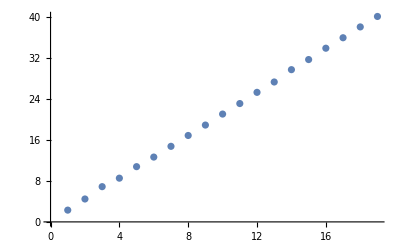

```mathematica
ListPlot[ComputingTime3Q3C]
```

```mathematica
ComputingTime3Q3C
FindFit[%,m x+b,{m,b},x]
```

{m→2.09482,b→0.189366}

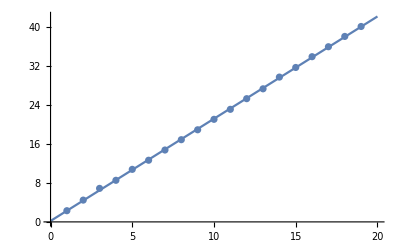

```mathematica
Show[Plot[m x+b/.{m->2.0948181596491233,b->0.1893657192982455},{x,0,20}],ListPlot[ComputingTime3Q3C]]
```

## To erase later:

```mathematica
ByteCount[PCEChannelsThreeQubitsFourComponents=If[PositivityTest[Reshuffle[PCESuperoperator[#]]]==True,,Nothing]&/@PCEsTauConfigurations[3,4][[1;;1000]]]/1000000000//N
```

1.2×10^-7

```mathematica
NumberOfPCEOperations[3,4]
```

39711

```mathematica
ThreeQ4CPCEsTaus=PCEsTauConfigurations[3,4];
PCEChannelsThreeQubitsFourComponents=ToExpression[Import["/home/jadeleon/Documents/projective_maps/ThreeQubitsFourComponentsPCEChannelsTaus.dat"]];
Do[
tau=Part[ThreeQ4CPCEsTaus,i];
CP=PositiveSemidefiniteMatrixQ[Reshuffle[PCESuperoperator[tau]]];
If[CP==True,AppendTo[PCEChannelsThreeQubitsFourComponents,tau]]
,{i,30001,39711}]
(*
Export["/home/jadeleon/Documents/projective_maps/ThreeQubitsFourComponentsPCEChannelsTaus.dat",PCEChannelsThreeQubitsFourComponents]*)
```

/home/jadeleon/Documents/projective_maps/ThreeQubitsFourComponentsPCEChannelsTaus.dat

```mathematica
PCEChannelsThreeQubitsFourComponents//Length
```

651

```mathematica
Quit[]
```

```mathematica
$HistoryLength=1;
```

```mathematica
PCEChannelsThreeQubitsFourComponents//Length
```

651

```mathematica
Quit[];Length[Range[10]]
```